# Triangular Lattice Model

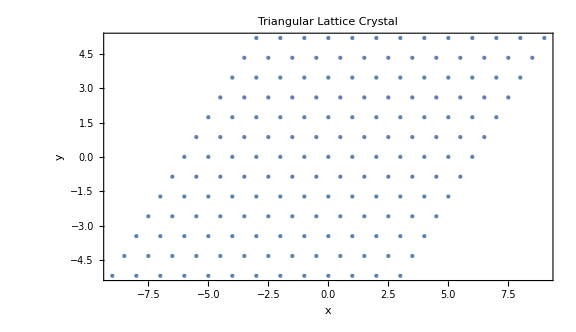

```mathematica
(* Define the lattice vector *)
A1={1,0}; 
A2={1/2,Sqrt[3]/2};
(* Number of lattice points in each direction *)
n=6; 
(* Lattice generation and visualization *)
TriX=Flatten[Table[A1*i+A2*j,{i,-n,n},{j,-n,n}],1];
plotLattice = ListPlot[TriX,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal", ImageSize->Large]
```

```mathematica
(* Parameters *)
t=1;           (* Hopping strength *)
J = 5;          (* Hund's coupling strength *)
ras = 0; (* Rashba coupling strength *)
```

```mathematica
(* Spin texture implimentation - Triple Q state of SkX*)
(* direction vectors of each spin helix in superposition *)
basisVectors = -1{{1,0}, {-1/2,Sqrt[3]/2}, {-1/2, -Sqrt[3]/2}};
(* The reciprocal space lattice vectors *)
QVectors =  Pi/(3 * Sqrt[3]){{2 Sqrt[3], 0},{-Sqrt[3], 3},{-Sqrt[3], -3}};
(* Initail phase or epoch *)
epoch={Pi/3,Pi/3,Pi/3};
(* Spin texture *)
mxy [x_, y_] := Total[Table[(Sin[QVectors[[i]].{x,y}+epoch[[i]] ]) basisVectors[[i]],{i,1,3}]]
mz[x_, y_] :=  Total[Table[(Cos[QVectors[[i]].{x,y} +epoch[[i]]]),{i,1,3}]]
(* Spin texture function to get the 3D tuples *)
spins[x_, y_] := {N[mxy[x, y].{1,0}],N[ mxy[x, y].{0,1}], N[mz[x,y]]}
```

```mathematica
(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{TriX[[i]][[1]],TriX[[i]][[2]],0},{i,1,Length[TriX]}];
(* Generating the spin texture and normalizing them *)
texture =Table[spins[TriX[[i]][[1]], TriX[[i]][[2]]],{i, 1, Length[TriX]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{0,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},{i,1,Length[TriX] }];

cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{0,1}]],
Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},{i,1,Length[TriX] }];

texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Full, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

```mathematica
(* Isolating single skyrmion position tuples *)
SkX = Table[If[Norm[TriX[[i]]]<=2, TriX[[i]]],{i, 1 , Length[TriX],1}];
SkX//MatrixForm;
UNITcell = DeleteCases[SkX,Null];
UNITcell // MatrixForm;
(* Getting the Unitcell tuples *)
For[i = 0,i<= 2,i++,
v = i *A1 + (2-i)*A2;
UNITcell = DeleteCases[UNITcell,v];
UNITcell= DeleteCases[UNITcell,{v[[1]], - v[[2]]}];
UNITcell = DeleteCases[UNITcell,{-i, - Sqrt[3]}];
] 
plotC1 = ListPlot[UNITcell,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal"];


UNITcell= Table[UNITcell[[i]]+{-2,0},{i,1,Length[UNITcell]}];
plotC2 = ListPlot[UNITcell,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal"];

(* Visualization of the isolated unitcell *)
OPvector = Table[{UNITcell[[i]][[1]],UNITcell[[i]][[2]],0},{i,1,Length[UNITcell]}];
sfield =Chop[N[Table[spins[UNITcell[[i]][[1]],UNITcell[[i]][[2]]],{i, 1, Length[UNITcell]}]]];
(* Spin texture in a unitcell *)
spinfield = Table[sfield[[i]]/Norm[sfield[[i]]],{i,1,Length[sfield]}];
cylinders1 = Table[
{{ColorData["Rainbow"][Rescale[spinfield[[i]][[3]],{0,1}]],Cylinder[{OPvector[[i]]-spinfield[[i]]/2,OPvector[[i]]},1/10]}},{i,1,Length[UNITcell] }
];
cones1= Table[
{{ColorData["Rainbow"][Rescale[spinfield[[i]][[3]],{0,1}]],
Cone[{OPvector[[i]],OPvector[[i]]+spinfield[[i]]/2},1/5]}},{i,1,Length[UNITcell] }
];
unitcellPLOT=Graphics3D[{cylinders1,cones1},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Small, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

```mathematica
(* Converting to Spherical Polar Coordinates *)
SpinPOLAR=CoordinateTransform["Cartesian"->"Spherical",spinfield]/.Indeterminate->0;
SpinPOLAR//MatrixForm;
SpinPOLAR = Table[If[SpinPOLAR[[i]][[3]]<0, {SpinPOLAR[[i]][[1]],SpinPOLAR[[i]][[2]],SpinPOLAR[[i]][[3]] + 2 Pi}, SpinPOLAR[[i]]],{i,1,Length[SpinPOLAR]}];
SpinPOLAR//MatrixForm
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

(1. | 0. | 0
1. | 0. | 0
1. | 0. | 0
1. | 0. | 0
1. | 1.85183 | 3.14159
1. | 1.85183 | 2.0944
1. | 0. | 0
1. | 1.85183 | 4.18879
1. | 3.14159 | 0
1. | 1.85183 | 1.0472
1. | 1.85183 | 5.23599
1. | 1.85183 | 0.)

```mathematica
(* Collecting the theta and phi values *)
θ =Table[SpinPOLAR[[i]][[2]],{i,1,Length[SpinPOLAR]}];
ϕ =Table[SpinPOLAR[[i]][[3]],{i,1,Length[SpinPOLAR]}];
(* Forming spin texture wavefunction, |χ⟩ := cos(θ/2)|↑⟩ + e^Iϕ sin(θ/2)|↓⟩*)
Ket := Table[{Chop[Cos[1/2 θ⟦i⟧]], Chop[Sin[1/2 θ⟦i⟧] ⅇ^(ⅈ ϕ⟦i⟧)]},{i,1,Length[UNITcell]}]
Ket// MatrixForm
(* The conjugate vector of the spin texture |χ⟩, ⟨χ|:=|χ⟩† *)
Bra := Table[Conjugate[Ket[[i]]],{i,1,Length[Ket]}]
Bra// MatrixForm
(* Neighbour table for Periodic Boundary condition Implimentation *)
NN1 = {5,6,7,8,9,10,1,11,12,4,2,3};
NN2 = {7,11,12,10,1,2,3,4,5,6,8,9};
NN3 = {2,3,8,5,6,7,11,9,10,1,12,4};
NN4 = {4,5,6,3,8,9,10,7,11,12,1,2};
NN5 = {11,12,4,1,2,3,8,5,6,7,9,10};
NN6 = {10,1,2,12,4,5,6,3,8,9,7,11};
```

(1. | 0
1. | 0
1. | 0
1. | 0
0.601103 | -0.799171
0.601103 | -0.399586+0.692103 ⅈ
1. | 0
0.601103 | -0.399586-0.692103 ⅈ
0 | 1.
0.601103 | 0.399586+0.692103 ⅈ
0.601103 | 0.399586-0.692103 ⅈ
0.601103 | 0.799171)

(1. | 0
1. | 0
1. | 0
1. | 0
0.601103 | -0.799171
0.601103 | -0.399586-0.692103 ⅈ
1. | 0
0.601103 | -0.399586+0.692103 ⅈ
0 | 1.
0.601103 | 0.399586-0.692103 ⅈ
0.601103 | 0.399586+0.692103 ⅈ
0.601103 | 0.799171)

```mathematica
K[kx_, ky_] := {kx, ky}
(* Hamiltonian matrix *)
Hij[kx_, ky_] := Module[{hopingProduct},
hopingProduct = ConstantArray[0,{2*Length[SpinPOLAR],2*Length[SpinPOLAR]}];
For[i = 1, i<= Length[SpinPOLAR], i++,
hopingProduct[[i]][[NN1[[i]]]] =  t ⅇ^(-ⅈ K[kx,ky].{1,0});
hopingProduct[[i]][[NN2[[i]]]] =  t ⅇ^(-ⅈ K[kx,ky].{-1,0});
hopingProduct[[i]][[NN3[[i]]]] =t ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2});
hopingProduct[[i]][[NN4[[i]]]] =t ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2});
hopingProduct[[i]][[NN5[[i]]]] = t ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2});
hopingProduct[[i]][[NN6[[i]]]] = t ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2});

hopingProduct[[i+12]][[NN1[[i]]]] =  I ras (-I) ⅇ^(-ⅈ K[kx,ky].{1,0});
hopingProduct[[i+12]][[NN2[[i]]]] =  I ras (I)ⅇ^(-ⅈ K[kx,ky].{-1,0});
hopingProduct[[i+12]][[NN3[[i]]]] =I ras ((√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2});
hopingProduct[[i+12]][[NN4[[i]]]] =I ras ((-√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2});
hopingProduct[[i+12]][[NN5[[i]]]] = I ras ((√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2});
hopingProduct[[i+12]][[NN6[[i]]]] = I ras ((-√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2});


hopingProduct[[i+12]][[NN1[[i]]+12]] =  t ⅇ^(-ⅈ K[kx,ky].{1,0});
hopingProduct[[i+12]][[NN2[[i]]+12]]=  t ⅇ^(-ⅈ K[kx,ky].{-1,0});
hopingProduct[[i+12]][[NN3[[i]]+12]] =t ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2});
hopingProduct[[i+12]][[NN4[[i]]+ 12]] =t ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2});
hopingProduct[[i+12]][[NN5[[i]]+12]] = t ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2});
hopingProduct[[i+12]][[NN6[[i]] + 12]] = t ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2});

hopingProduct[[i]][[NN1[[i]]+12]] =  I ras (I) ⅇ^(-ⅈ K[kx,ky].{1,0});
hopingProduct[[i]][[NN2[[i]]+12]]=  I ras (-I)ⅇ^(-ⅈ K[kx,ky].{-1,0});
hopingProduct[[i]][[NN3[[i]]+12]] =I ras ((√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2});
hopingProduct[[i]][[NN4[[i]]+ 12]] =I ras ((-√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2});
hopingProduct[[i]][[NN5[[i]]+12]] =  I ras ((√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2});
hopingProduct[[i]][[NN6[[i]] + 12]] = I ras ((-√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2});

hopingProduct[[i]][[i]] = -J Cos[θ[[i]]] ;
hopingProduct[[i+12]][[i+12]] = J Cos[θ[[i]]];
hopingProduct[[i]][[i+12]] = -J Sin[θ[[i]]]*E^(-I ϕ[[i]] ) ;
hopingProduct[[i+12]][[i]] = -J Sin[θ[[i]]]*E^(I ϕ[[i]] );];
hopingProduct
]
Hij[kx, ky]// MatrixForm;
ConjugateTranspose[Hij[1,1]]== Hij[1,1]
(* Eigenvalue function *)
Ev[kx_,ky_] := Sort[Eigenvalues[Hij[kx, ky]] ]
```

True

```mathematica
(* Eigenvalue function *)
Ev[kx_,ky_] := Sort[Eigenvalues[Hij[kx,ky]] ]
(* Collection of Eigen values along the irreducible path in the reciprocal space *)
d=25; (* step count *)
tabGK[n_]:=Table[Ev[k,k/(√3)][[n]],{k,0, Pi/(3),Pi/(3 * 2*d)}];
tabKM[n_]:=Table[Ev[π/3,ky][[n]],{ky,Pi/(3 √3),0,-Pi/(3 √3 d)}];
tabMG[n_]:=Table[Ev[kx,0][[n]],{kx,Pi/(3),0,-Pi/(3* Sqrt[3] d)}];

l1=Length[tabGK[1]];
l2=l1+Length[tabKM[1]];
l3=l2+Length[tabMG[1]];
customTicksX={{0,Style["Γ",Bold]},{l1,Style["K",Bold]},{l2,Style["M",Bold]},{l3,Style["Γ",Bold]}};
vl1=Graphics[{Line[{{l1,-20},{l1,20}}]},AspectRatio->1];
vl2=Graphics[{Line[{{l2,-20},{l2,20}}]},AspectRatio->1];
```

```mathematica
band1=Join[tabGK[1],tabKM[1],tabMG[1]];
band2=Join[tabGK[2],tabKM[2],tabMG[2]];
band3=Join[tabGK[3],tabKM[3],tabMG[3]];
band4=Join[tabGK[4],tabKM[4],tabMG[4]];
band5=Join[tabGK[5],tabKM[5],tabMG[5]];
band6=Join[tabGK[6],tabKM[6],tabMG[6]];
band7=Join[tabGK[7],tabKM[7],tabMG[7]];
band8=Join[tabGK[8],tabKM[8],tabMG[8]];
band9=Join[tabGK[9],tabKM[9],tabMG[9]];
band10=Join[tabGK[10],tabKM[10],tabMG[10]];
band11=Join[tabGK[11],tabKM[11],tabMG[11]];
band12=Join[tabGK[12],tabKM[12],tabMG[12]];
band13=Join[tabGK[13],tabKM[13],tabMG[13]];
band14=Join[tabGK[14],tabKM[14],tabMG[14]];
band15=Join[tabGK[15],tabKM[15],tabMG[15]];
band16=Join[tabGK[16],tabKM[16],tabMG[16]];
band17=Join[tabGK[17],tabKM[17],tabMG[17]];
band18=Join[tabGK[18],tabKM[18],tabMG[18]];
band19=Join[tabGK[19],tabKM[19],tabMG[19]];
band20=Join[tabGK[20],tabKM[20],tabMG[20]];
band21=Join[tabGK[21],tabKM[21],tabMG[21]];
band22=Join[tabGK[22],tabKM[22],tabMG[22]];
band23=Join[tabGK[23],tabKM[23],tabMG[23]];
band24=Join[tabGK[24],tabKM[24],tabMG[24]];
```

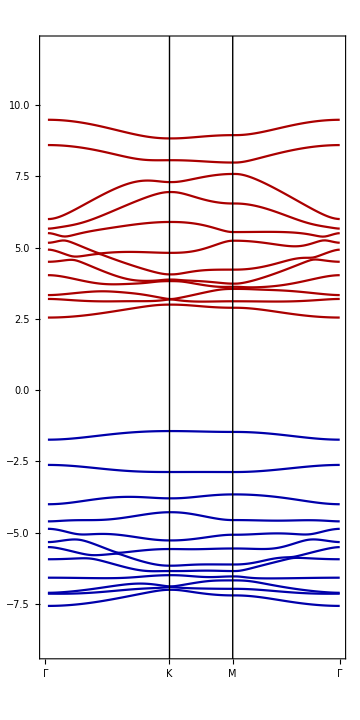

```mathematica
customTicksX={{0,Style["Γ",Bold]},{l1,Style["K",Bold]},{l2,Style["M",Bold]},{l3,Style["Γ",Bold]}};
plot1=ListLinePlot[{band1,band2,band3,band4,band5,band6,band7,band8,band9,band10,band11,band12},PlotStyle->{Darker[Blue]},ImageSize->Medium,AspectRatio->6/3,PlotRange->{{0,l3},{-9, 12}},FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True,FrameTicksStyle->Directive[Bold,Black]];
plot2=ListLinePlot[{ band13, band14, band15, band16,band17,band18,band19,band20,band21,band22,band23,band24},PlotStyle->{Darker[Red]},ImageSize->Medium,AspectRatio->6/3,PlotRange->{{0,l3},{-9, 12}},FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True,FrameTicksStyle->Directive[Bold,Black]];
Show[plot1, plot2,vl1,vl2, BaseStyle->{FontSize-> 16},Background->White, ImageResolution->500]
```

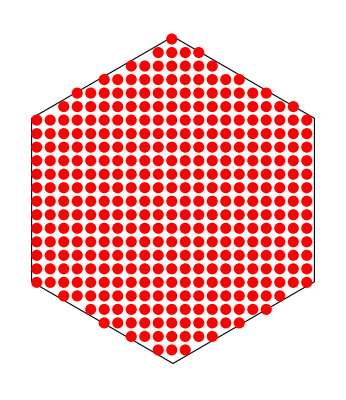

{381,2}

```mathematica
(*Side length of the hexagon*)
sideLength=(2 π)/(3 Sqrt[3]);
(*Define the hexagonal domain*)
hexagon=Polygon[Table[sideLength {Sin[2 π k/6],Cos[2 π k/6]},{k,6}]];
(*Distance between grid points*)
distance=0.1;
(*Generate a grid of points within the hexagon*)
kpoint=Select[Flatten[Table[{x,y},{x,-sideLength,sideLength,distance},{y,-sideLength,sideLength,distance}],1],RegionMember[hexagon,#]&];
(*Display the hexagon and grid points*)
Graphics[{{EdgeForm[Black],FaceForm[],hexagon},{Red,PointSize[0.02],Point[kpoint]}}]

kpoint//Dimensions
```

```mathematica
band3d[i_] :=Table[Ev[kpoint[[j]][[1]], kpoint[[j]][[2]]][[i]],{j,1,Length[kpoint]}]
bands =Flatten[ Table[Flatten[band3d[i]],{i, 1,2*Length[UNITcell]}]];
```

```mathematica
SortedEVectors[kx_, ky_]:= Module[{eigenvalues, eigenvectors, SEvalue, SEvector, SEvectorC},
{eigenvalues,eigenvectors}=Eigensystem[Hij[kx, ky]];
{SEvalue,SEvector}=Transpose[SortBy[Transpose[{eigenvalues,eigenvectors}],First]];
SEvectorC = SEvector//Chop;
For[i=1, i<=2*Length[UNITcell], i++,
SEvectorC[[i]]  = SEvectorC[[i]]/Norm[SEvectorC[[i]]];
];
SEvectorC// Chop
];
(* Derivatives definition *)
Hdx[kxval_, kyval_] := Module[{hopingProduct, kx, ky},
hopingProduct = ConstantArray[0,{2*Length[UNITcell],2*Length[UNITcell]}];
For[i = 1, i<= Length[UNITcell], i++,
hopingProduct[[i]][[NN1[[i]]]] =  D[t ⅇ^(-ⅈ K[kx,ky].{1,0}),kx];
hopingProduct[[i]][[NN2[[i]]]] =  D[t ⅇ^(-ⅈ K[kx,ky].{-1,0}),kx];
hopingProduct[[i]][[NN3[[i]]]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),kx];
hopingProduct[[i]][[NN4[[i]]]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),kx];
hopingProduct[[i]][[NN5[[i]]]] =D[ t ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),kx];
hopingProduct[[i]][[NN6[[i]]]] = D[t ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),kx];

hopingProduct[[i+12]][[NN1[[i]]]] =  D[I ras (-I) ⅇ^(-ⅈ K[kx,ky].{1,0}),kx];
hopingProduct[[i+12]][[NN2[[i]]]] =  D[I ras (I)ⅇ^(-ⅈ K[kx,ky].{-1,0}),kx];
hopingProduct[[i+12]][[NN3[[i]]]] =D[I ras ((√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),kx];
hopingProduct[[i+12]][[NN4[[i]]]] =D[I ras ((-√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),kx];
hopingProduct[[i+12]][[NN5[[i]]]] = D[I ras ((√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),kx];
hopingProduct[[i+12]][[NN6[[i]]]] = D[I ras ((-√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),kx];


hopingProduct[[i+12]][[NN1[[i]]+12]] =  D[t ⅇ^(-ⅈ K[kx,ky].{1,0}),kx];
hopingProduct[[i+12]][[NN2[[i]]+12]]=  D[t ⅇ^(-ⅈ K[kx,ky].{-1,0}),kx];
hopingProduct[[i+12]][[NN3[[i]]+12]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),kx];
hopingProduct[[i+12]][[NN4[[i]]+ 12]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),kx];
hopingProduct[[i+12]][[NN5[[i]]+12]] = D[t ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),kx];
hopingProduct[[i+12]][[NN6[[i]] + 12]] = D[t ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),kx];

hopingProduct[[i]][[NN1[[i]]+12]] = D[ I ras (I) ⅇ^(-ⅈ K[kx,ky].{1,0}),kx];
hopingProduct[[i]][[NN2[[i]]+12]]= D[ I ras (-I)ⅇ^(-ⅈ K[kx,ky].{-1,0}),kx];
hopingProduct[[i]][[NN3[[i]]+12]] =D[I ras ((√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),kx];
hopingProduct[[i]][[NN4[[i]]+ 12]] =D[I ras ((-√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),kx];
hopingProduct[[i]][[NN5[[i]]+12]] = D[ I ras ((√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),kx];
hopingProduct[[i]][[NN6[[i]] + 12]] =D[ I ras ((-√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),kx];

hopingProduct[[i]][[i]] = 0 ;
hopingProduct[[i+12]][[i+12]] =0;
hopingProduct[[i]][[i+12]] = 0 ;
hopingProduct[[i+12]][[i]] =0;];
hopingProduct/.{kx-> kxval, ky-> kyval}
]
Hdy[kxval_, kyval_] := Module[{hopingProduct, kx, ky},
hopingProduct = ConstantArray[0,{2*Length[UNITcell],2*Length[UNITcell]}];
For[i = 1, i<= Length[UNITcell], i++,
hopingProduct[[i]][[NN1[[i]]]] =  D[t ⅇ^(-ⅈ K[kx,ky].{1,0}),ky];
hopingProduct[[i]][[NN2[[i]]]] =  D[t ⅇ^(-ⅈ K[kx,ky].{-1,0}),ky];
hopingProduct[[i]][[NN3[[i]]]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),ky];
hopingProduct[[i]][[NN4[[i]]]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),ky];
hopingProduct[[i]][[NN5[[i]]]] =D[ t ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),ky];
hopingProduct[[i]][[NN6[[i]]]] = D[t ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),ky];

hopingProduct[[i+12]][[NN1[[i]]]] =  D[I ras (-I) ⅇ^(-ⅈ K[kx,ky].{1,0}),ky];
hopingProduct[[i+12]][[NN2[[i]]]] =  D[I ras (I)ⅇ^(-ⅈ K[kx,ky].{-1,0}),ky];
hopingProduct[[i+12]][[NN3[[i]]]] =D[I ras ((√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),ky];
hopingProduct[[i+12]][[NN4[[i]]]] =D[I ras ((-√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),ky];
hopingProduct[[i+12]][[NN5[[i]]]] = D[I ras ((√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),ky];
hopingProduct[[i+12]][[NN6[[i]]]] = D[I ras ((-√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),ky];


hopingProduct[[i+12]][[NN1[[i]]+12]] =  D[t ⅇ^(-ⅈ K[kx,ky].{1,0}),ky];
hopingProduct[[i+12]][[NN2[[i]]+12]]=  D[t ⅇ^(-ⅈ K[kx,ky].{-1,0}),ky];
hopingProduct[[i+12]][[NN3[[i]]+12]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),ky];
hopingProduct[[i+12]][[NN4[[i]]+ 12]] =D[t ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),ky];
hopingProduct[[i+12]][[NN5[[i]]+12]] = D[t ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),ky];
hopingProduct[[i+12]][[NN6[[i]] + 12]] = D[t ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),ky];

hopingProduct[[i]][[NN1[[i]]+12]] = D[ I ras (I) ⅇ^(-ⅈ K[kx,ky].{1,0}),ky];
hopingProduct[[i]][[NN2[[i]]+12]]= D[ I ras (-I)ⅇ^(-ⅈ K[kx,ky].{-1,0}),ky];
hopingProduct[[i]][[NN3[[i]]+12]] =D[I ras ((√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(√3)/2}),ky];
hopingProduct[[i]][[NN4[[i]]+ 12]] =D[I ras ((-√3)/2+I/2)ⅇ^(-ⅈ K[kx,ky].{1/2,(-√3)/2}),ky];
hopingProduct[[i]][[NN5[[i]]+12]] = D[ I ras ((√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(√3)/2}),ky];
hopingProduct[[i]][[NN6[[i]] + 12]] =D[ I ras ((-√3)/2-I/2)ⅇ^(-ⅈ K[kx,ky].{-1/2,(-√3)/2}),ky];

hopingProduct[[i]][[i]] = 0 ;
hopingProduct[[i+12]][[i+12]] =0;
hopingProduct[[i]][[i+12]] = 0 ;
hopingProduct[[i+12]][[i]] =0;];
hopingProduct/.{kx-> kxval, ky-> kyval}
]
(* Berry connection for band *)
bconnection[kx_,ky_,bandindex_]:=Module[{sum,nket,newarray,dHx,dHy,otherev ,bandev,mket,ediff},
bandev=Ev[kx,ky][[bandindex]];
otherev = Delete[Ev[kx,ky],bandindex];
nket=SortedEVectors[kx,ky][[bandindex]];
mket=Delete[SortedEVectors[kx,ky],bandindex];
dHx=Hdx[kx,ky];
dHy=Hdy[kx,ky];
ediff[i_]:=(bandev-otherev[[i]]);
sum=Table[(-(Conjugate[nket].(dHx.mket[[i]]))*(Conjugate[mket[[i]]].(dHy.nket))+(Conjugate[nket].(dHy.mket[[i]]))*(Conjugate[mket[[i]]].(dHx.nket)))/ediff[i]^2,{i,1,Length[mket]}];
sum//Total//Im];

B[bandindex_]:= Flatten[Table[bconnection[kpoint[[j]][[1]], kpoint[[j]][[2]],bandindex],{j, 1, Length[kpoint]}]]
```

```mathematica
Berry =Flatten[ Table[B[i],{i, 1, 2*Length[UNITcell]}]];
```

```mathematica
(* Kubo formula implimentation *)
conductivity[ef_, KT_, bands_, berry_] := Module[{energies, bclist, term, result},
{energies,bclist}=Transpose[Select[Transpose[{bands,berry}],#[[1]]<=ef&]];
term = Table[bclist⟦i⟧/(1+ⅇ^((energies⟦i⟧-ef)/KT)),{i, 1, Length[energies]}];

result = Total[term];
result   //Chop
]
```

```mathematica
Ef = Table[i,{i, -11, 12, 1/100}];
Kt = 0.00000001;
```

```mathematica
sigma1 = Table[{Ef[[i]],conductivity[Ef[[i]], Kt, bands, Berry]2Pi/(Length[kpoint]*6*√3)},{i, 1, Length[Ef]}];
```

Set::shape: Lists {energies$827543,bclist$827543} and {} are not the same shape.

Set::shape: Lists {energies$827546,bclist$827546} and {} are not the same shape.

Set::shape: Lists {energies$827549,bclist$827549} and {} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

General::munfl: Exp[-856403.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-322421.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103342.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

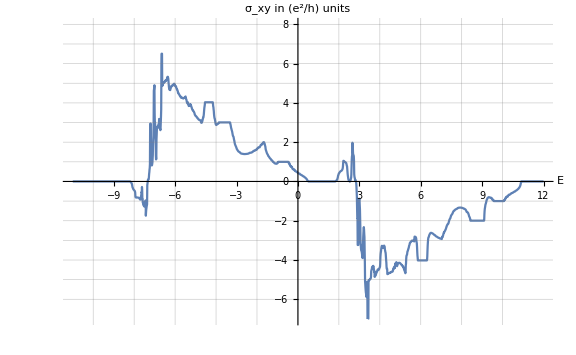

```mathematica
ListLinePlot[sigma1 , GridLines->{ {-10,-8,-6,-4,-2,0,2,4,6,8,10},{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8}}, PlotRange->{{-11,12},{-7,8}}, BaseStyle->{FontSize-> 20},Background->White,ImageSize->Large,AxesLabel->{"E","σ_xy in (e^2/h) units"}]
```